```mathematica
Tninv[ω_] :=(39/14)*1/(1+ⅈ*ω*10^(-3))
Tinv[ω_]:= -1/(14/25+ⅈ*ω*56*10^(-5))
```

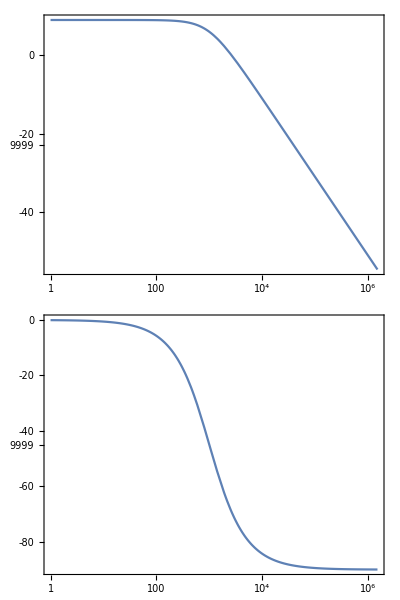

```mathematica
BodePlot[Tninv[ω], {ω, 1, 1500000}]
```

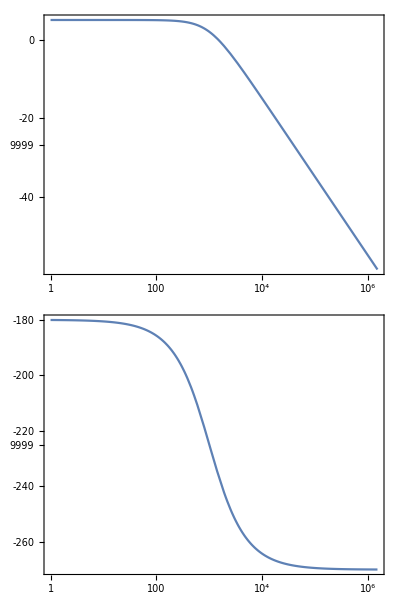

```mathematica
BodePlot[Tinv[ω], {ω, 1, 1500000}]
```

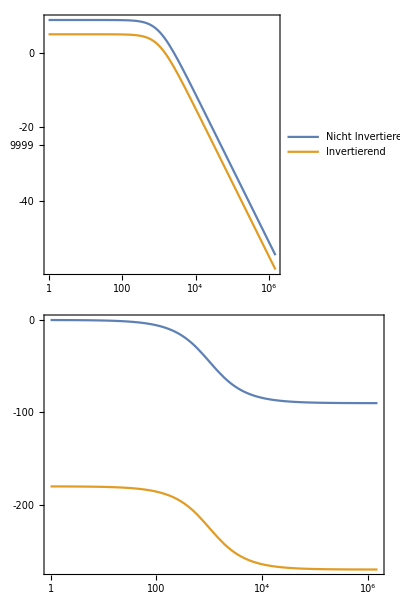

```mathematica
BodePlot[{Tninv[ω], Tinv[ω]}, {ω, 1, 1500000},PlotLegends->{"Nicht Invertierend","Invertierend"}]
```